```mathematica
SetDirectory["C:/Users/serha/OneDrive - Jacobs University/courses/3rd semester/Advance_Project_II/20201124_network_generation_with_Lifting/"];
```

```mathematica
data=Import["C:/Users/serha/OneDrive - Jacobs University/courses/3rd semester/Advance_Project_II/20200825_indicative_features/cgl_data_csp_sequences_only.csv",HeaderLines->1];
```

```mathematica
rawaim=data[[All,110]];
aim=DeleteCases[rawaim,"NA"];
campaign=Delete[data[[All,118]],Position[rawaim,"NA"]];
productionorder=Delete[data[[All,4]],Position[rawaim,"NA"]];
Print["unique aim data members: ",Dimensions@DeleteDuplicates@aim]
Print["aim data length: ",Dimensions@aim]
Print["amount of production order ID's: ",Dimensions@DeleteDuplicates@productionorder]
Print["amount of customer ID's: ",Dimensions@DeleteDuplicates@Delete[data[[All,6]],Position[rawaim,"NA"]]]
Print["sequence data groups amount: ",Dimensions@DeleteDuplicates@campaign]
```

unique aim data members: {2138}

aim data length: {32098}

amount of production order ID's: {5873}

amount of customer ID's: {399}

sequence data groups amount: {738}

```mathematica
range=Range[824,1000];
check=Table[Mod[32098,i],{i,range}]
min=Min[check]
pos=Position[Table[Mod[32098,i],{i,range}],min(*Min[Table[Mod[32098,i],{i,Range[500,600]}]]*)][[1]]
bucketsize=range[[pos]]
```

{786,748,710,672,634,596,558,520,482,444,406,368,330,292,254,216,178,140,102,64,26,833,796,759,722,685,648,611,574,537,500,463,426,389,352,315,278,241,204,167,130,93,56,19,850,814,778,742,706,670,634,598,562,526,490,454,418,382,346,310,274,238,202,166,130,94,58,22,878,843,808,773,738,703,668,633,598,563,528,493,458,423,388,353,318,283,248,213,178,143,108,73,38,3,886,852,818,784,750,716,682,648,614,580,546,512,478,444,410,376,342,308,274,240,206,172,138,104,70,36,2,913,880,847,814,781,748,715,682,649,616,583,550,517,484,451,418,385,352,319,286,253,220,187,154,121,88,55,22,962,930,898,866,834,802,770,738,706,674,642,610,578,546,514,482,450,418,386,354,322,290,258,226,194,162,130,98}

2

{121}

{944}

```mathematica
bins=Table[MinMax[i],{i,Partition[Sort[aim],bucketsize]}]
```

{{0.311705,0.40181},{0.40181,0.4315},{0.4315,0.466007},{0.466007,0.483225},{0.483225,0.513741},{0.513741,0.580606},{0.580712,0.641147},{0.641147,0.72534},{0.72534,0.748049},{0.748049,0.815316},{0.815316,0.86596},{0.86596,0.886195},{0.886195,0.898956},{0.898956,0.918147},{0.918147,1.05187},{1.05247,1.11764},{1.11764,1.12124},{1.12124,1.14077},{1.14077,1.1673},{1.1673,1.18808},{1.18808,1.36641},{1.36641,1.40016},{1.40016,1.41495},{1.41495,1.43808},{1.43808,1.47438},{1.47438,1.52499},{1.52499,1.7346},{1.7346,1.75697},{1.7585,1.79994},{1.79994,2.20415},{2.20415,2.46071},{2.46071,2.48965},{2.48965,2.55051},{2.55051,2.98738}}

```mathematica
binning=Table[Catch[Do[If[IntervalMemberQ[Interval[i],aim[[j]]]==True,Throw[i]],
{i,bins}]],{j,Length[aim]}];
```

```mathematica
Position[binning,Null]
```

{}

```mathematica
aim=binning;
binningmembers=Sort[DeleteDuplicates[aim]];
Print["binning amount: ",Dimensions@DeleteDuplicates@binning]
Print["dimension of binned data: ",Dimensions@aim]
Print["binning members dimension : ",Dimensions@binningmembers]
```

binning amount: {34,2}

dimension of binned data: {32098,2}

binning members dimension : {34,2}

```mathematica
aimbaskets=Values@GroupBy[Thread[{aim,campaign}],Last->First];
aimbasketsrev=Table[DeleteDuplicates[i],{i,aimbaskets}];
productionorderbaskets=Values@GroupBy[Thread[{productionorder,aim}],Last->First];
productionorderbasketsrev=Table[DeleteDuplicates[i],{i,productionorderbaskets}];
Print["counts of unique prod. order id's in each binning group: ",KeySort@Counts@Table[Length[i],{i,productionorderbasketsrev}]]
Print["binning groups association to count of unique prod. order id's: ",KeySort@MapThread[#1->#2&,{Keys@GroupBy[Thread[{productionorder,aim}],Last->First],Table[Length[i],{i,productionorderbasketsrev}]}]]
Print["binning groups association to count of their total members: ",KeySort@Counts@aim]
Print["binning amount: ",Dimensions@DeleteDuplicates@aim]
```

counts of unique prod. order id's in each binning group: <|38→1,55→1,62→1,78→1,105→1,107→1,114→1,117→1,129→1,133→1,160→1,161→1,165→1,167→1,171→1,182→1,186→1,191→1,194→1,197→1,198→1,200→1,201→1,202→1,203→1,212→1,223→1,227→1,228→1,237→1,238→2,242→1,312→1|>

binning groups association to count of unique prod. order id's: <|{0.311705,0.40181}→165,{0.40181,0.4315}→78,{0.4315,0.466007}→242,{0.466007,0.483225}→182,{0.483225,0.513741}→117,{0.513741,0.580606}→238,{0.580712,0.641147}→237,{0.641147,0.72534}→312,{0.72534,0.748049}→227,{0.748049,0.815316}→201,{0.815316,0.86596}→198,{0.86596,0.886195}→212,{0.886195,0.898956}→186,{0.898956,0.918147}→160,{0.918147,1.05187}→133,{1.05247,1.11764}→191,{1.11764,1.12124}→62,{1.12124,1.14077}→129,{1.14077,1.1673}→171,{1.1673,1.18808}→202,{1.18808,1.36641}→203,{1.36641,1.40016}→105,{1.40016,1.41495}→107,{1.41495,1.43808}→167,{1.43808,1.47438}→238,{1.47438,1.52499}→200,{1.52499,1.7346}→161,{1.7346,1.75697}→114,{1.7585,1.79994}→197,{1.79994,2.20415}→223,{2.20415,2.46071}→55,{2.46071,2.48965}→38,{2.48965,2.55051}→194,{2.55051,2.98738}→228|>

binning groups association to count of their total members: <|{0.311705,0.40181}→946,{0.40181,0.4315}→1086,{0.4315,0.466007}→811,{0.466007,0.483225}→950,{0.483225,0.513741}→960,{0.513741,0.580606}→911,{0.580712,0.641147}→957,{0.641147,0.72534}→953,{0.72534,0.748049}→951,{0.748049,0.815316}→953,{0.815316,0.86596}→930,{0.86596,0.886195}→927,{0.886195,0.898956}→974,{0.898956,0.918147}→908,{0.918147,1.05187}→943,{1.05247,1.11764}→1141,{1.11764,1.12124}→862,{1.12124,1.14077}→930,{1.14077,1.1673}→855,{1.1673,1.18808}→936,{1.18808,1.36641}→966,{1.36641,1.40016}→980,{1.40016,1.41495}→1015,{1.41495,1.43808}→847,{1.43808,1.47438}→924,{1.47438,1.52499}→944,{1.52499,1.7346}→950,{1.7346,1.75697}→922,{1.7585,1.79994}→951,{1.79994,2.20415}→977,{2.20415,2.46071}→929,{2.46071,2.48965}→942,{2.48965,2.55051}→947,{2.55051,2.98738}→920|>

binning amount: {34,2}

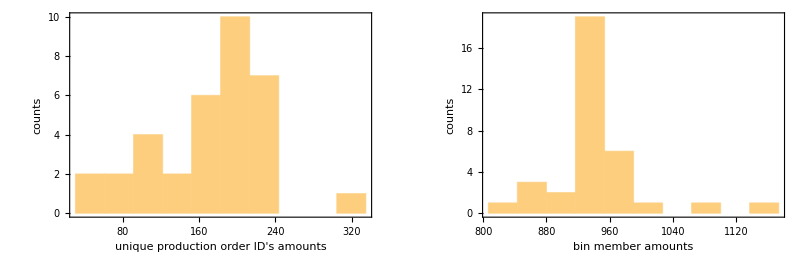

```mathematica
GraphicsRow[{Histogram[KeySort@MapThread[#1->#2&,{Keys@GroupBy[Thread[{productionorder,aim}],Last->First],Table[Length[i],{i,productionorderbasketsrev}]}],{"Raw",10},Frame->True,FrameLabel->{"unique production order ID's amounts","counts"},ImageSize->Full(*,PlotLabel->"Unique Production Order ID Counts for Each Bin"*)],Histogram[KeySort@Counts@aim,{"Raw",10},Frame->True,FrameLabel->{"bin member amounts","counts"},ImageSize->Full(*,PlotLabel->"Total Members Counts for Each Bin"*)]}]
```

```mathematica
AbsoluteTiming[singlesupportvalues=Table[N[Count[Table[MemberQ[i,j],{i,aimbasketsrev}],True]/Length[aimbasketsrev]],{j,binningmembers}];]
pairs=Subsets[binningmembers,{2}];
Dimensions[binningmembers]
Dimensions[pairs]
Dimensions[aimbasketsrev]
AbsoluteTiming[pairsupportvalues=Table[N[Count[Table[SubsetQ[i,j],{i,aimbasketsrev}],True]/
Length[aimbasketsrev]],{j,pairs}];]
AbsoluteTiming[liftvalues=pairsupportvalues/(DeleteCases[Flatten@UpperTriangularize[Table[singlesupportvalues[[j]]*singlesupportvalues[[k]],{j,Length[binningmembers]},{k,Length[binningmembers]}],1],0.]);]
allmatrixelements=Sort[Join[pairs,Reverse[pairs,2],Table[{i,i},{i,binningmembers}]]];
```

{0.140987,Null}

{34,2}

{561,2,2}

{738}

{6.45779,Null}

{0.0016487,Null}

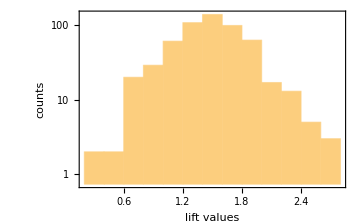

```mathematica
Histogram[liftvalues,ScalingFunctions->"Log",PlotRange->All,Frame->True,FrameLabel->{"lift values","counts"},ImageSize->Medium]
```

{508,2,2}

{0.0942128,Null}

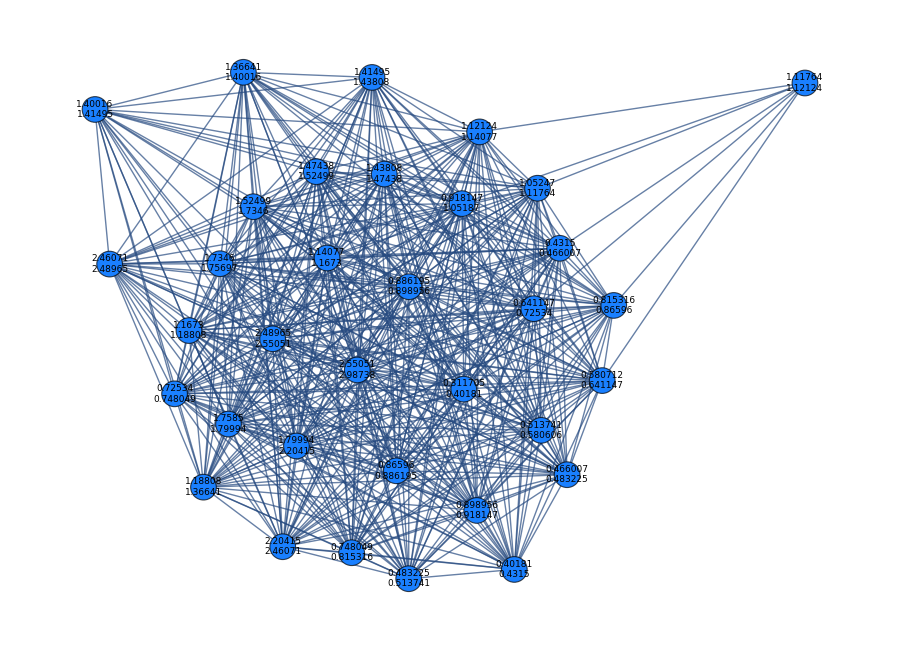

```mathematica
likelypairs=Extract[pairs,Position[liftvalues,x_/;x>1]];
Dimensions@likelypairs
AbsoluteTiming[binarymatrix=ArrayReshape[Table[If[j==True,1,0],{j,Table[MemberQ[likelypairs,i],{i,allmatrixelements}]}],{Length@binningmembers,Length@binningmembers}];]
graph=AdjacencyGraph[binarymatrix,{GraphLayout->"SpringEmbedding",DirectedEdges->False,EdgeShapeFunction->"Line",VertexSize->0.5,VertexStyle->RGBColor[0.1,0.5,1.],VertexLabelStyle->Directive[Black,Italic,9],VertexLabels->Flatten[MapThread[{#1->Placed[#2,Center]}&,{Range[1,Dimensions[binarymatrix][[1]]],
Table[StringRiffle[i,"\n"],{i,binningmembers}]}]]},ImageSize->900]
```